```mathematica
m[R_]:=-(η+ϵ-ϵ*R)+√((η+ϵ-ϵ*R)^2+4*R*ϵ*η)
```

```mathematica
n[R_]:=(((m[R]^2+4η*m[R]+2*ϵ*m[R]+4η^2+4*ϵ*η+4η)^2-4*(2*m[R]^3+12*η*m[R]^2+24*η^2*m[R]+8*ϵ*η*m[R]+16*η^3+16*ϵ*η^2)))/4(m[R]+2η)
```

```mathematica
ϵ=0.001
```

0.001

```mathematica
R=4.5
```

4.5

```mathematica
η=1
```

1

```mathematica
Clear[R,ϵ,η]
```

```mathematica
Solve[n[R]==0,R]
```

{{R→-1000. (-1.0005+1. η)-0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))-0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+8.×10^6 (-1.0005+1. η)^2-3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)-(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)-1. (4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)-(0.25 (-6.4×10^10 (-1.0005+1. η)^3+16000. (-1.0005+1. η) (11993.-1.0002×10^7 η+6.×10^6 η^2)-8. (-11984.+5.98001×10^6 η-7.99799×10^9 η^2+4.×10^9 η^3)))/(√(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))))},{R→-1000. (-1.0005+1. η)-0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))+0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+8.×10^6 (-1.0005+1. η)^2-3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)-(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)-1. (4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)-(0.25 (-6.4×10^10 (-1.0005+1. η)^3+16000. (-1.0005+1. η) (11993.-1.0002×10^7 η+6.×10^6 η^2)-8. (-11984.+5.98001×10^6 η-7.99799×10^9 η^2+4.×10^9 η^3)))/(√(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))))},{R→-1000. (-1.0005+1. η)+0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))-0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+8.×10^6 (-1.0005+1. η)^2-3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)-(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)-1. (4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(0.25 (-6.4×10^10 (-1.0005+1. η)^3+16000. (-1.0005+1. η) (11993.-1.0002×10^7 η+6.×10^6 η^2)-8. (-11984.+5.98001×10^6 η-7.99799×10^9 η^2+4.×10^9 η^3)))/(√(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))))},{R→-1000. (-1.0005+1. η)+0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))+0.5 √(-11993.+1.0002×10^7 η-6.×10^6 η^2+8.×10^6 (-1.0005+1. η)^2-3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)-(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)-1. (4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(0.25 (-6.4×10^10 (-1.0005+1. η)^3+16000. (-1.0005+1. η) (11993.-1.0002×10^7 η+6.×10^6 η^2)-8. (-11984.+5.98001×10^6 η-7.99799×10^9 η^2+4.×10^9 η^3)))/(√(-11993.+1.0002×10^7 η-6.×10^6 η^2+4.×10^6 (-1.0005+1. η)^2+3.33333×10^-7 (1.1993×10^10-1.0002×10^13 η+6.×10^12 η^2)+(1.11111×10^-13 (2.498×10^13-1.6792×10^23 η+1.60641×10^25 η^2))/(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3)+(4.62408-2.06242×10^11 η+8.00542×10^18 η^2-2.38463×10^18 η^3+1.85185×10^-20 √(0.-4.30447×10^51 η+1.15798×10^62 η^2+9.31056×10^69 η^3+1.86872×10^77 η^4-1.10813×10^77 η^5))^(1/3))))}}

```mathematica
p[η_]:=-1000. (-1.0004995+1. η)+0.5 √(-11992.998001+1.0001992*^7 η-6.*^6 η^2+4.*^6 (-1.0004995+1. η)^2+3.3333333333333335*^-7 (1.1992998001*^10-1.0001992*^13 η+6.*^12 η^2)+(1.1111111111111111*^-13 (2.4980013996001*^13-1.67920207776072*^23 η+1.6064096064016*^25 η^2))/(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)+(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3))-0.5 √(-11992.998001+1.0001992*^7 η-6.*^6 η^2+8.*^6 (-1.0004995+1. η)^2-3.3333333333333335*^-7 (1.1992998001*^10-1.0001992*^13 η+6.*^12 η^2)-(1.1111111111111111*^-13 (2.4980013996001*^13-1.67920207776072*^23 η+1.6064096064016*^25 η^2))/(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)-1. (4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)+(0.25 (-6.4*^10 (-1.0004995+1. η)^3+16000. (-1.0004995+1. η) (11992.998001-1.0001992*^7 η+6.*^6 η^2)-8. (-11984.004+5.980006*^6 η-7.99799*^9 η^2+4.*^9 η^3)))/(√(-11992.998001+1.0001992*^7 η-6.*^6 η^2+4.*^6 (-1.0004995+1. η)^2+3.3333333333333335*^-7 (1.1992998001*^10-1.0001992*^13 η+6.*^12 η^2)+(1.1111111111111111*^-13 (2.4980013996001*^13-1.67920207776072*^23 η+1.6064096064016*^25 η^2))/(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)+(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3))))
```

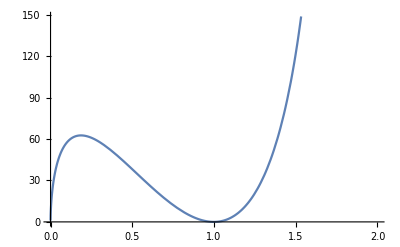

```mathematica
Plot[p[η],{η,0,2}]
```

```mathematica
q[η_]:=-1000. (-1.0004995+1. η)+0.5 √(-11992.998001+1.0001992*^7 η-6.*^6 η^2+4.*^6 (-1.0004995+1. η)^2+3.3333333333333335*^-7 (1.1992998001*^10-1.0001992*^13 η+6.*^12 η^2)+(1.1111111111111111*^-13 (2.4980013996001*^13-1.67920207776072*^23 η+1.6064096064016*^25 η^2))/(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)+(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3))+0.5 √(-11992.998001+1.0001992*^7 η-6.*^6 η^2+8.*^6 (-1.0004995+1. η)^2-3.3333333333333335*^-7 (1.1992998001*^10-1.0001992*^13 η+6.*^12 η^2)-(1.1111111111111111*^-13 (2.4980013996001*^13-1.67920207776072*^23 η+1.6064096064016*^25 η^2))/(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)-1. (4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)+(0.25 (-6.4*^10 (-1.0004995+1. η)^3+16000. (-1.0004995+1. η) (11992.998001-1.0001992*^7 η+6.*^6 η^2)-8. (-11984.004+5.980006*^6 η-7.99799*^9 η^2+4.*^9 η^3)))/(√(-11992.998001+1.0001992*^7 η-6.*^6 η^2+4.*^6 (-1.0004995+1. η)^2+3.3333333333333335*^-7 (1.1992998001*^10-1.0001992*^13 η+6.*^12 η^2)+(1.1111111111111111*^-13 (2.4980013996001*^13-1.67920207776072*^23 η+1.6064096064016*^25 η^2))/(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3)+(4.624079071556555-2.062421735600884*^11 η+8.005422302167106*^18 η^2-2.3846281955911255*^18 η^3+1.851851851851852*^-20 √(0.-4.304473719849384*^51 η+1.1579798327231442*^62 η^2+9.310560963543854*^69 η^3+1.8687163598282242*^77 η^4-1.1081262971389465*^77 η^5))^(1/3))))
```

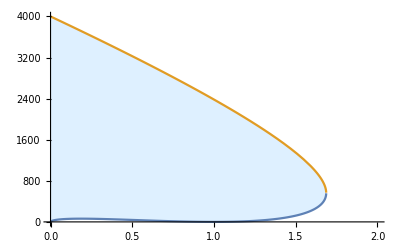

```mathematica
Plot[{p[η],q[η]},{η,0,2},Filling->{1->{{2},{LightBlue,White}}}]
```

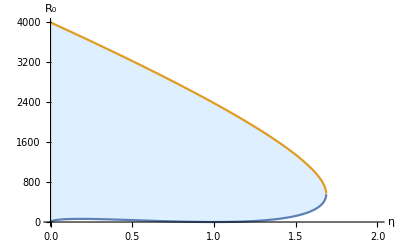

```mathematica
Show[%22,AxesLabel->{HoldForm[η],HoldForm[Subscript[R, 0]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```